Exercises for Section 22 | Machine Learning

Identify what language the word “ajatella” comes from. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

Apply ImageIdentify to an image of a tiger, getting the image using ctrl+=. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageIdentify[EntityValue[LinguisticAssistant,"Image"]]
```

tiger

Make a table of image identifications for an image of a tiger, blurred by an amount from 1 to 5. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageIdentify[Table[Blur[-Graphics-,n],{n,1,5}]]
```

{tiger,tiger,tiger,spiny-finned fish,fish}

"ToExpression::sntxi: Incomplete expression; more input is needed .
"

```mathematica
Entity["Species","Species:PantheraTigris"][EntityProperty["Species","Image"]]
```

-Graphics-

```mathematica
Table[ImageIdentify[Blur[Entity["Species","Species:PantheraTigris"][EntityProperty["Species","Image"]]]],{n,1,5}]
```

{tiger,tiger,tiger,tiger,tiger}

Classify the sentiment of “I’m so happy to be here”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

Find the 10 words in WordList[ ] that are nearest to “happy”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

Generate 20 random numbers up to 1000 and find which 3 are nearest to 100. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[Table[RandomInteger[1000],20],100,3]
```

{122,46,275}

Generate a list of 10 random colors, and find which 5 are closest to Red. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[Table[RandomColor[],10],RGBColor[1,0,0],5]
```

{RGBColor[0.7601617269112655, 0.19020882515748538, 0.033992513664584445],RGBColor[0.5624401695198438, 0.3182595200598841, 0.18427653749569606],RGBColor[0.28806710565450455, 0.5942173826887376, 0.4679930490130193],RGBColor[0.26323088260401484, 0.6223204578799282, 0.3433832319638137],RGBColor[0.6948063129499777, 0.2229887802702497, 0.9747681208706982]}

Of the first 100 squares, find the one nearest to 2000. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
First[Nearest[Table[n^2,{n,100}],2000]]
```

2025

Find the 3 European flags nearest to the flag of Brazil. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

Make a graph of the 2 nearest neighbors of each color in Table[Hue[h],{h,0,1,.05}]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graph[Nearest[Table[Hue[h],{h,0,1,0.05}],Table[Hue[h],{h,0,1,0.05}]
```

Graph[{{Hue[0.0],Hue[1.0]},{Hue[0.05],Hue[0.0]},{Hue[0.1],Hue[0.05]},{Hue[0.15000000000000002],Hue[0.2]},{Hue[0.2],Hue[0.25]},{Hue[0.25],Hue[0.30000000000000004]},{Hue[0.30000000000000004],Hue[0.35000000000000003]},{Hue[0.35000000000000003],Hue[0.30000000000000004]},{Hue[0.4],Hue[0.35000000000000003]},{Hue[0.45],Hue[0.4]},{Hue[0.5],Hue[0.45]},{Hue[0.55],Hue[0.5]},{Hue[0.6000000000000001],Hue[0.65]},{Hue[0.65],Hue[0.7000000000000001]},{Hue[0.7000000000000001],Hue[0.65]},{Hue[0.75],Hue[0.7000000000000001]},{Hue[0.8],Hue[0.75]},{Hue[0.8500000000000001],Hue[0.8]},{Hue[0.9],Hue[0.8500000000000001]},{Hue[0.9500000000000001],Hue[0.0]},{Hue[0.0],Hue[1.0]}}]

Nearest::near1: Hue[0.] is neither a list of real points nor a valid list of rules.

Nearest::near1: Hue[0.05] is neither a list of real points nor a valid list of rules.

Nearest::near1: Hue[0.1] is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

{Nearest[Hue[0.0],2],Nearest[Hue[0.05],2],Nearest[Hue[0.1],2],Nearest[Hue[0.15000000000000002],2],Nearest[Hue[0.2],2],Nearest[Hue[0.25],2],Nearest[Hue[0.30000000000000004],2],Nearest[Hue[0.35000000000000003],2],Nearest[Hue[0.4],2],Nearest[Hue[0.45],2],Nearest[Hue[0.5],2],Nearest[Hue[0.55],2],Nearest[Hue[0.6000000000000001],2],Nearest[Hue[0.65],2],Nearest[Hue[0.7000000000000001],2],Nearest[Hue[0.75],2],Nearest[Hue[0.8],2],Nearest[Hue[0.8500000000000001],2],Nearest[Hue[0.9],2],Nearest[Hue[0.9500000000000001],2],Nearest[Hue[1.0],2]}

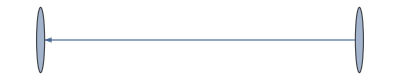

-Graphics-

```mathematica
Graph[Table[Hue[h],{h,0,1,0.05}]->Flatten[Nearest[Table[Hue[h],{h,0,1,0.05}],{Red,Green,Blue}]]]
Graph[{Table[Hue[h],{h,0,1,0.05}]->Table[Hue[h],{h,0,1,0.06}]}]
```

```mathematica
Graph[{Table[Hue[h],{h,0,1,0.05}]->{1,2,3,4}}]
```

-Graphics-

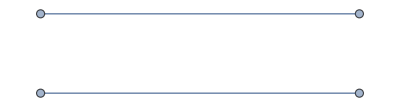

```mathematica
UndirectedGraph[Flatten[{RGBColor[1,1,0]->RGBColor[0,1,0.6],RGBColor[0,0,1]->RGBColor[0.5,0.5,0.5]}]]
```

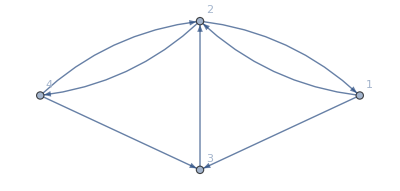

```mathematica
Graph[{1->2,3->2,2->1,4->2,2->4,4->3,1->3},VertexLabels->All]
```

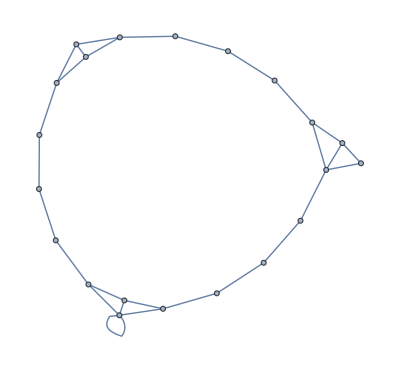

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2,VertexLabels->All]
```

```mathematica
Dendrogram[Table[Hue[h],{h,0,1,0.05}]]
```

-Graphics-

Generate a list of 100 random numbers from 0 to 100, and make a graph of the 2 nearest neighbors of each one. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

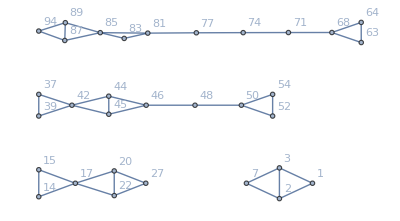

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],40],2,VertexLabels->All]
```

Collect the flags of Asia into clusters of similar flags. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]];
```

```mathematica
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]];
```

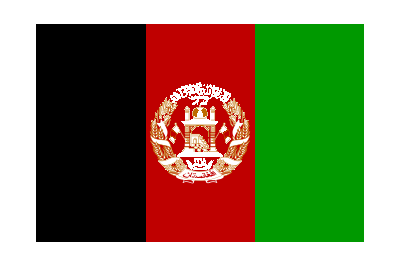
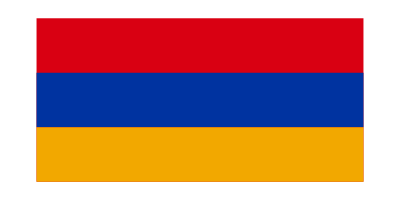
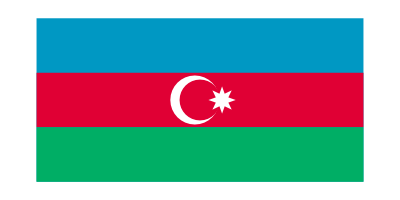
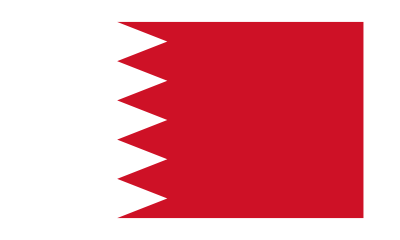
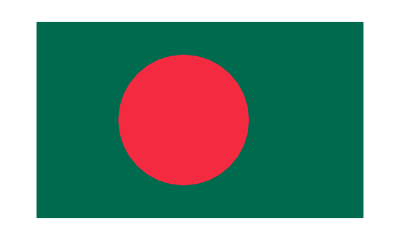
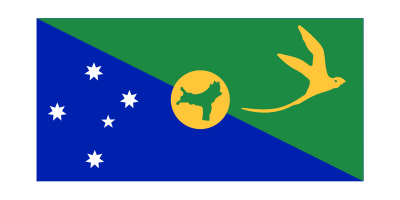
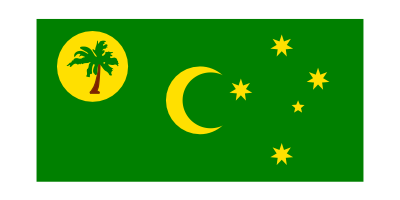
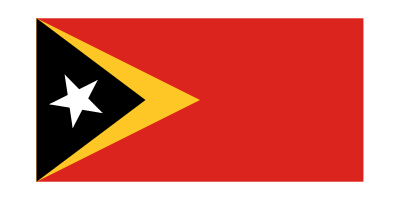

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[EntityValue[EntityClass["Country","Asia"],EntityProperty["Country","Flag"]]]
```

Make raster images of the letters of the alphabet at size 20, then make a graph of the 2 nearest neighbors of each one. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
NearestNeighborGraph[Table[Rasterize[Style[FromLetterNumber[n],20]],{n,1,26,1}],2,VertexLabels->All]
```

-Graphics-

Generate a table of the results of using TextRecognize on “hello” rasterized at size 50 and then blurred by between 1 and 10. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TextRecognize[Table[Blur[Rasterize[Style["hello",50]],n],{n,1,10}]]
```

{hello,hello,hello,hello,hello,hello,hello,hello,hello,hello}

```mathematica
TextRecognize[Table[Rasterize[Blur[Style["hello",50],n]],{n,1,10}]]
```

Blur::imginv: Expecting an image or graphics instead of hello.

General::stop: Further output of Blur::imginv will be suppressed during this calculation.

{shell,shell,shell,shell,shell,shell,shell,shell,shell,Blur | hello. 10|}

```mathematica
Table[TextRecognize[Blur[Rasterize[Style["hello",50]],b]],{b,1,10}]
```

{hello,hello,hello,hello,hello,hello,hello,hello,hello,hello}

Make a dendrogram for images of the first 10 letters of the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Dendrogram[Rasterize[Take[Alphabet[],{1,10}]]]
```

Dendrogram::smldat: The dataset should contain at least two elements.

Dendrogram[-Graphics-]

```mathematica
Dendrogram[Table[Rasterize[FromLetterNumber[n]],{n,10}]]
```

-Graphics-

Make a feature space plot for the uppercase letters of the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FeatureSpacePlot[Rasterize[ToUpperCase[FromLetterNumber[Range[26]]]]]
```

DimensionReduction::mlmpty: The dataset should contain at least one example.

FeatureSpacePlot[-Graphics-]

```mathematica
FeatureSpacePlot[Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]]
```

-Graphics-

Make a table of image identifications for a picture of the Eiffel Tower, blurred by an amount from 1 to 5. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[ImageIdentify[Blur[Entity["Building","EiffelTower::5h9w8"]["Image"],b]],{b,1,5,1}]
```

{Eiffel Tower,Eiffel Tower,tower,stupa,stupa}

```mathematica
EntityProperty[Entity["Building","EiffelTower"],"Image"]
```

EntityProperty[Entity[Building,EiffelTower],Image]

Classify the sentiment of the Wikipedia article on “happiness”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Classify["Sentiment",WikipediaData["happiness"]]
```

Neutral

Of colors in the list Table[Hue[h],{h,0,1,.05}], find which are the 3 nearest to Pink. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[Table[Hue[h],{h,0,1,0.05}],Pink,3]
```

{Hue[0.9500000000000001],Hue[0.9],Hue[0.05]}

Compute all fractions i/j for i and j up to 500, and find the 10 fractions closest to pi. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Nearest[Table[i/j,{i,500},{j,500}],Pi,10]
```

Nearest::dmtch: The dimension of «1» and π does not match.

Nearest[{1},π,10]
 |  |  |  |

```mathematica
Nearest[Flatten[Table[i/j,{i,500},{j,500}]],Pi,10]
```

{355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155}

Generate a list of 10 random numbers from 0 to 10, and make a graph of the 3 nearest neighbors of each one. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

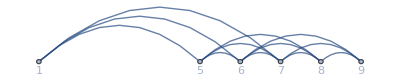

```mathematica
NearestNeighborGraph[Table[RandomInteger[10],10],3,VertexLabels->All]
```

Find clusters of similar colors in a list of 100 random colors. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
FindClusters[Table[RandomColor[],100]]
```

{{RGBColor[0.460085441210216, 0.044442559232549694, 0.19497935922761434],RGBColor[0.6427773912296395, 0.14397833559988715, 0.1220364160408216],RGBColor[0.6688235968267642, 0.015628591178031837, 0.20981372626069406],RGBColor[0.5283922854401881, 0.05157225870569171, 0.11621198539458422]},{RGBColor[0.24101704568820348, 0.5990104578154658, 0.15436655650463815],RGBColor[0.3318277079854697, 0.9308945889550451, 0.19605251273661772],RGBColor[0.16366150691765702, 0.6933174686566179, 0.7899613595284058],RGBColor[0.6372948697647303, 0.6583656756129306, 0.5051341962696712],RGBColor[0.06469423744375025, 0.792976816178427, 0.5695805280121247],RGBColor[0.4290808462802691, 0.626066442543654, 0.5778295750754412],RGBColor[0.006082230612352024, 0.5392458015750863, 0.35211001449944535],RGBColor[0.9761992571702753, 0.9862078057303314, 0.006621599104774667],RGBColor[0.5268022228898697, 0.46799099110251885, 0.419625235558017],RGBColor[0.20666578474698483, 0.5698618753152631, 0.6670524561628564],RGBColor[0.21981669909893786, 0.9508799275073156, 0.3969580162138677],RGBColor[0.3649905092119292, 0.8613359235360907, 0.3055608891822663],RGBColor[0.14984659716531357, 0.6535836824227457, 0.8079267600122988],RGBColor[0.3255137529525205, 0.8017544023278622, 0.3415103436724858],RGBColor[0.8290781472774653, 0.9747148574901012, 0.4902000410484657],RGBColor[0.14579603302101507, 0.9501952848676343, 0.7852209822958289],RGBColor[0.051912529791583895, 0.7611029650197696, 0.9150917322990353],RGBColor[0.39796377359278234, 0.9062641545029211, 0.19003283595266418],RGBColor[0.567491167270318, 0.7389633570669265, 0.8058294955054623],RGBColor[0.216972775088619, 0.5626961149745064, 0.24036096255830053],RGBColor[0.3911666812877461, 0.8948836181347517, 0.2115407058031462],RGBColor[0.2727667736994608, 0.8576765543395792, 0.26786311215360104],RGBColor[0.5750657278194564, 0.6971451098790762, 0.6931640706962809],RGBColor[0.7090263012438383, 0.8541242278799812, 0.07179590013876136],RGBColor[0.515310159065332, 0.47980347883751895, 0.35015051262310815],RGBColor[0.15103784840915346, 0.79782161392223, 0.36133000001109306],RGBColor[0.06515693092975683, 0.7328478408680377, 0.8242251881556943],RGBColor[0.7567890520386436, 0.9817607752659885, 0.23325145031006533],RGBColor[0.049384907503663644, 0.5671072916569582, 0.6541505917906414],RGBColor[0.3396080654364779, 0.5074686758170384, 0.5087205898676184],RGBColor[0.4601672106264354, 0.6167667323618782, 0.465994160933209],RGBColor[0.280238311895878, 0.8694271276931593, 0.9257585094495253],RGBColor[0.29360306006563497, 0.6360643996896183, 0.509534723027248],RGBColor[0.618676024104285, 0.795208977624529, 0.19218984694458108],RGBColor[0.8272202643210167, 0.9756331611726514, 0.4361046031931932],RGBColor[0.42014963954607154, 0.9397479295828342, 0.19091589747101678],RGBColor[0.15874357201445521, 0.8085009592242502, 0.8295668908560954],RGBColor[0.5624461795192395, 0.9447004742326692, 0.2829548344727326],RGBColor[0.05448623843622724, 0.8850656356052942, 0.5715477035715462]},{RGBColor[0.7858303158423605, 0.5617792429575676, 0.35150686414880083],RGBColor[0.6860068815587863, 0.5403903607482703, 0.18878057701168305],RGBColor[0.6114994676837311, 0.6136288685056646, 0.21940332771966964],RGBColor[0.972262394244217, 0.732845831052974, 0.01458141869793006],RGBColor[0.8351908601127256, 0.5862766059506117, 0.03281925103116201],RGBColor[0.8615013312392172, 0.6477609073241104, 0.26386773334632907]},{RGBColor[0.8024475610934547, 0.3714236346790383, 0.3197295566319873],RGBColor[0.7402754233652828, 0.3191912465980935, 0.3364725944355422],RGBColor[0.7294234417363805, 0.37134108408668554, 0.2744522486041685],RGBColor[0.7329517944078969, 0.3817714031872703, 0.25804847874372827]},{RGBColor[0.734134925369319, 0.3799951396421921, 0.7362017871132529],RGBColor[0.5064011861162021, 0.2206400338912795, 0.9032285556032795],RGBColor[0.5985271706220847, 0.10222114887063816, 0.7289934077070173],RGBColor[0.5892574643287027, 0.4193071854228654, 0.9671241107819808],RGBColor[0.3369399171630345, 0.15343157629617932, 0.662760980019302],RGBColor[0.7269751609717017, 0.27114801911773423, 0.9089088052518888],RGBColor[0.18116070991940325, 0.12600655244188763, 0.5923226139536417],RGBColor[0.2005769721745636, 0.2459558117880909, 0.787689224283525],RGBColor[0.4317173753950745, 0.29599197604990857, 0.6886756629261983],RGBColor[0.44684562463694455, 0.2540495893882171, 0.7875883681235034],RGBColor[0.4022474026088809, 0.2848224105825441, 0.708881224545528],RGBColor[0.5608348448172935, 0.18793674297320617, 0.7085453568704776],RGBColor[0.632085056066974, 0.15035168888603012, 0.6582118429321404],RGBColor[0.008061696276095986, 0.09490178418246886, 0.8897480822230217]},{RGBColor[0.8752254089637597, 0.4474788294537011, 0.6899944241768625],RGBColor[0.8449925177802506, 0.5536065028767796, 0.7001411450045247],RGBColor[0.33973494198936915, 0.03991523298638833, 0.3439549190217468],RGBColor[0.17152489138622884, 0.08474656375137757, 0.28396402483219774],RGBColor[0.950137764580707, 0.21654500487368233, 0.4668710588807281],RGBColor[0.7096136901513364, 0.366296519337878, 0.5526153065150647],RGBColor[0.6326043116297702, 0.20513671270706713, 0.5023532639605282],RGBColor[0.4088124532713162, 0.007751180355936915, 0.3699472543586595],RGBColor[0.8261462972784339, 0.5682814757451691, 0.6260472958400896],RGBColor[0.7850384326967419, 0.06600674439101173, 0.4161763440178363],RGBColor[0.8539887204831791, 0.4585824931176321, 0.5634441437203606],RGBColor[0.7314431454439208, 0.09176776886651883, 0.47631265704739345],RGBColor[0.7575247583714091, 0.6241200505769331, 0.6839507589061109]},{RGBColor[0.27457017659066874, 0.42969088190362026, 0.7361839404434225],RGBColor[0.056354706947445266, 0.5890515558362979, 0.9899594129504987],RGBColor[0.28339579000594517, 0.5747004399631701, 0.8681452291335072],RGBColor[0.33812173462939965, 0.5181945436482849, 0.9502733274486701]},{RGBColor[0.9548291636248825, 0.041547213324512944, 0.3014547358145192],RGBColor[0.9584138006043912, 0.011728386067402896, 0.3112716328011269]},{RGBColor[0.9311243890003544, 0.5163864266874278, 0.29216155975472824],RGBColor[0.8798347686254961, 0.2783217402537057, 0.030122845765510498],RGBColor[0.832323089794726, 0.4720274802170521, 0.17472983258053398]},{RGBColor[0.1480024298940934, 0.10811001914056373, 0.018708052147937027],RGBColor[0.2689803088308398, 0.1234042330477938, 0.14114191115992525],RGBColor[0.29825955491774314, 0.2818556208109948, 0.29374517833457636],RGBColor[0.022045554679983592, 0.18616237911826694, 0.217682730490248],RGBColor[0.26007051694381844, 0.16900072436415448, 0.19136440797274523],RGBColor[0.01594458210778371, 0.004080416217193905, 0.06031240612972],RGBColor[0.13302690472529388, 0.1992274446775124, 0.26916034993750815]},{RGBColor[0.10638354473576417, 0.35923181350734534, 0.14483118937195205],RGBColor[0.11155443914183172, 0.27239187060274284, 0.07858495483449834]},{RGBColor[0.8605637174037661, 0.7544493787746334, 0.48261181042963797],RGBColor[0.8063701069417719, 0.7898529436139594, 0.4969781284097414]}}

Make a feature space plot for both upper and lowercase letters of the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
{Rasterize[Alphabet[]],Rasterize[ToUpperCase[Alphabet[]]]}
```

{-Graphics-,-Graphics-}

```mathematica
Table[{Rasterize[FromLetterNumber[n]],Rasterize[ToUpperCase[FromLetterNumber[n]]]},{n,1,26,1}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
FeatureSpacePlot[Join[Table[Rasterize[FromLetterNumber[n]],{n,1,26}],Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,1,26}]]]
```

-Graphics-